```mathematica
Quit[];
```

```mathematica
1+1//Timing
```

{7.×10^-6,2}

```mathematica
<<"/Users/noahsteinberg/Library/Mathematica/Applications/DsixTools/DsixTools.m"
```

DsixTools 1.1.3

by Alejandro Celis, Javier Fuentes-Martin, Avelino Vicente and Javier Virto

Reference: arXiv:1704.04504

Website: https://dsixtools.github.io/

This program is free software: you can redistribute it and/or modify it under the terms of the GNU General Public License as published by the Free Software Foundation, either version 3 of the License, or any later version.

See ?DsixTools`* for a list of routines and variables.

## Options

```mathematica
LOWSCALE=173.21;
HIGHSCALE=10000;

CPV=0;
ReadRGEs=1;
RGEsMethod=1;
ExportRGEs=0;
UseRGEsSM=1;
exportSMEFTrunner=0;
exportEWmatcher=0;
exportWETrunner=0;
inputWCsType=1;

Init[g]=e/Sin[θW];
Init[gp]=e/Cos[θW];
Init[gs]=Sqrt[4Pi (0.108057)];
Init[λ]=mh^2/v^2;
Init[m2]=mh^2/2;
Init[GU[1,1]]=1.23231*10^-5;
Init[GU[1,2]]=-1.64215*10^-3;
Init[GU[1,3]]=5.90635*10^-3;
Init[GU[2,1]]=2.84527*10^-6;
Init[GU[2,2]]=7.10724*10^-3;
Init[GU[2,3]]=-4.18547*10^-2;
Init[GU[3,1]]=4.65426*10^-8;
Init[GU[3,2]]=3.08758*10^-4;
Init[GU[3,3]]=0.994858;
Init[GD[1,1]]=2.70195*10^-5;
Init[GD[1,2]]=0;
Init[GD[1,3]]=0;
Init[GD[2,1]]=0;
Init[GD[2,2]]=5.51888*10^-4;
Init[GD[2,3]]=0;
Init[GD[3,1]]=0;
Init[GD[3,2]]=0;
Init[GD[3,3]]=2.403012*10^-2;
Init[GE[1,1]]=2.93766*10^-6;
Init[GE[1,2]]=0;
Init[GE[1,3]]=0;
Init[GE[2,1]]=0;
Init[GE[2,2]]=6.07422*10^-4;
Init[GE[2,3]]=0;
Init[GE[3,1]]=0;
Init[GE[3,2]]=0;
Init[GE[3,3]]=1.02157*10^-2;
Init[θ]=0;
Init[θp]=0;
Init[θs]=0;
```

## Here we are going to run our wilson coefficients in the SMEFT from 10TeV down to M_Top using DSixTools. First we set our Wilson coefficients Input values at μ = tHIGH = 10 TeV

```mathematica
initalwilson = .0000005;

Init[DUQL[1,2,1,3]]= initalwilson;
Init[DUQL[1,2,2,3]]=initalwilson;
Init[DUQL[1,2,3,3]]=initalwilson;
```

## Create input values

```mathematica
SetDirectory[NotebookDirectory[]];
WriteAndReadInputFiles["Options_program2.dat","WCsInput_program2.dat","SMInput_program2.dat"];
```

Input : SMEFT Wilson coefficients

Input : SMEFT Wilson coefficients

Input : SMEFT Wilson coefficients

```mathematica
LoadModule["SMEFTrunner"]
LoadBetaFunctions;
RunRGEsSMEFT;
```

LoadModule::Already: Warning : SMEFTrunner module already loaded

Loading SMEFT β functions

Running

Running finished!

## Results after SMEFTrunner

```mathematica
(* We find the position of Subscript[(Subscript[C, ll]), 1112] in Parameters *)
param1 = FindParameterSMEFT[DUQL[1,2,1,3]];
param2 = FindParameterSMEFT[DUQL[1,2,2,3]];
param3 = FindParameterSMEFT[DUQL[1,2,3,3]];
```

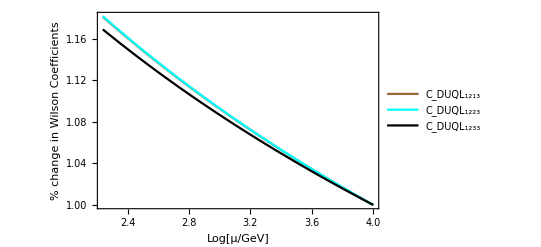

```mathematica
(* Plot % Change in Wilson coefficients as a function of μ, We normalize each plot by the value of the initial wilson coefficient (1 x10^-7 in this case)*) 

plotWC7=Plot[(1/initalwilson)outSMEFTrunner[[param1]],{t,tLOW,tHIGH},Frame->True,Axes->False,PlotRange->{{tLOW,tHIGH},Automatic},FrameLabel->{"Log[μ/GeV]","% change in (C_DUQL)_1213",None,None}, PlotLegends->{"C_DUQL_1213"}, PlotStyle->{Brown}, PlotRange->Automatic];
plotWC8 =Plot[(1/initalwilson)outSMEFTrunner[[param2]], {t,tLOW,tHIGH},Frame->True,Axes->False,PlotRange->{{tLOW,tHIGH},Automatic},FrameLabel->{"Log[μ/GeV]","% change in (C_DUQL)_1223",None,None}, PlotLegends->{"C_DUQL_1223"}, PlotStyle->{Cyan}, PlotRange->Automatic];
plotWC9 = Plot[(1/initalwilson)outSMEFTrunner[[param3]], {t,tLOW,tHIGH},Frame->True,Axes->False,PlotRange->{{tLOW,tHIGH},Automatic},FrameLabel->{"Log[μ/GeV]","% change in (C_DUQL)_1233",None,None}, PlotLegends->{"C_DUQL_1233"}, PlotStyle->{Black}, PlotRange->Automatic];

Show[plotWC7, plotWC8, plotWC9,PlotRange->Automatic,Frame->True, FrameLabel->{"Log[μ/GeV]","% change in Wilson Coefficients"}]
```

Now match the 3 above wilson coefficients at M_Top to the single wilson coefficient in the WET at M_Top

```mathematica
Subscript[V, 11]= .97427;
Subscript[V, 21] = .22520;
Subscript[V, 31] = .00867;
Subscript[V, 12] = .22534;
Subscript[V, 22] = .97344;
Subscript[V, 32] = .0404;
Subscript[V, 13] = .00351;
Subscript[V, 23] = .0412;
Subscript[V, 33] = .999146;

matchC= -( Subscript[V, 11](outSMEFTrunner[[param1]]/.t->tLOW) + Subscript[V, 21](outSMEFTrunner[[param2]]/.t->tLOW) + Subscript[V, 31](outSMEFTrunner[[param3]]/.t->tLOW));
matchC
```

{-7.13636×10^-7}

Now we have our WET wilson coefficient at M_Top and we want to run this down to 1 GeV

```mathematica
<<"/Users/noahsteinberg/Desktop/BNV_Mathematica_Programs/RunDec.m"
```

RunDec: a Mathematica package for running and decoupling of the

strong coupling and quark masses

by K.G. Chetyrkin, J.H. K\"uhn and M. Steinhauser (January 2000)

by F. Herren and M. Steinhauser (April 2016, v2.1)

```mathematica
ALRQCDtop[mt_, MZ_, mb_, mc_, p0_, as5MZ_]:= Module[{as5mt, as5mb, as4mb, as4mc, as3mc,as3p0},
as5mt = AlphasExact[as5MZ, MZ, mt, 5, 4];
as5mb = AlphasExact[as5MZ,MZ,mb,5,4];
as4mb = DecAsDownMS[as5mb, mb, mb, 4, 4];
as4mc = AlphasExact[as4mb,mb, mc, 4, 4];
as3mc = DecAsDownMS[as4mc, mc, mc, 3, 4];
as3p0 = AlphasExact[as3mc, mc, p0, 3, 4];
Return[(as3p0/as3mc)^(6/27)(as4mc/as4mb)^(6/25)(as5mb/as5mt)^(6/23)((as3p0 + (9π)/16)/(as3mc + (9π)/16))^(-29/144)((as4mc + (50π)/77)/(as4mb + (50π)/77))^(-173/825)((as5mb + (23π)/29)/(as5mt + (23π)/29))^(-430/2001)];]
```

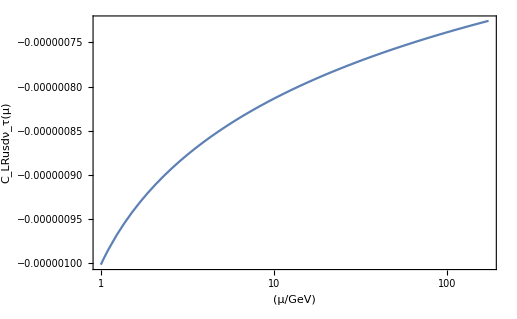

```mathematica
CusdnutauLR = LogLinearPlot[matchC*ALRQCDtop[173.21, 91.1876, 4.18, 1.28,  p, 0.1185], {p, 1.0, 173.21}, Frame->True, FrameLabel->{"(μ/GeV)", "C_LRusdν_τ(μ)"}]
```

```mathematica
ALRQCDtop[173.21, 91.1876, 4.18, 1.28, 1.0, 0.1185]
```

1.40406

Here I want to compare the running in the SMEFT of the wilson coefficients using DSixTools(gauge + yukawa contribution to running) vs 1loop QCD vs 2loop QCD

```mathematica
<<"/Users/noahsteinberg/Desktop/BNV_Mathematica_Programs/RunDec.m"
b1[Nfl_, Ncl_]:= (-(11Ncl - 2Nfl))/3;
b2[Nfl_, Ncl_]:= -34/3 Ncl^2 + 10/3 Ncl Nfl + 2((Ncl^2 - 1)/(2  Ncl))Nfl;
Δ = -10/3;
AQCDRL1loop[MX_, mt_, MZ_, as5MZ_, p0_]:= Module[{as5mt, as6mt, as6p0, as6mx}, (*I'm going to set a fake value for Subscript[α, s] at Mtop*)
as5mt = AlphasExact[as5MZ, MZ, mt, 5, 4];
as6mt = DecAsUpOS[as5mt, mt, mt, 5, 4];
as6mx = AlphasExact[0.11810043533097503, mt, MX, 6, 4];
as6p0 = AlphasExact[0.11810043533097503, mt, p0, 6, 4];
Return[(as6p0/as6mx)^(-2/b1[6,3])];]
```

RunDec: a Mathematica package for running and decoupling of the

strong coupling and quark masses

by K.G. Chetyrkin, J.H. K\"uhn and M. Steinhauser (January 2000)

by F. Herren and M. Steinhauser (April 2016, v2.1)

```mathematica
AQCDRL2loop[MX_, mt_, MZ_, as5MZ_, p0_]:= Module[{as5mt, as6mt, as6p0,as6mx},(*I'm going to set a fake value for Subscript[α, s] at Mtop*)
as5mt = AlphasExact[as5MZ, MZ, mt, 5, 4];
as6mt = DecAsUpOS[as5mt, mt, mt, 5, 4];
as6mx = AlphasExact[0.11810043533097503, mt, MX, 6, 4];
as6p0 = AlphasExact[0.11810043533097503, mt, p0, 6, 4];
Return[(as6p0/as6mx)^(-2/b1[6,3])((as6p0 + (4π b1[6,3])/b2[6,3])/(as6mx + (4π b1[6,3])/b2[6,3]))^(2/b1[6,3] - (42 + 24 + 9Δ)/(18b2[6,3]))];]
```

```mathematica
LR1loop = 
Plot[AQCDRL1loop[10000, 173.21, 91.1876, 0.1182, 10^logp0], {logp0,Log10[173.21], 4}, Frame->True, FrameLabel->{"log(μ/GeV)", "% change in Wilson Coefficient"}, PlotStyle->{Green},  PlotLegends->{"1 loop QCD only"}];
```

```mathematica
LR2loop = 
Plot[AQCDRL2loop[10000, 173.21, 91.1876, 0.1182, 10^logp0], {logp0, Log10[173.21], 4}, Frame->True, FrameLabel->{"log_10(μ/GeV)", "% change in Wilson Coefficient"}, PlotStyle->{Red}, PlotLegends->{"2 loop QCD only"}];
```

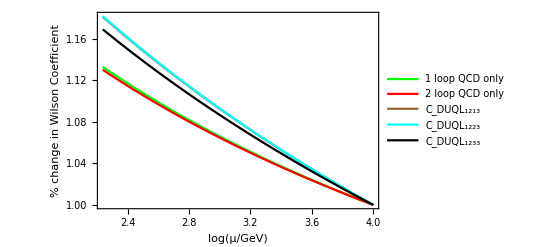

```mathematica
Show[LR1loop, LR2loop,plotWC7, plotWC8, plotWC9 , PlotRange->All]
```

```mathematica
FindParameterSMEFT[g]
```

{1}

```mathematica
outSMEFTrunner[[1]]/.t->tHIGH
```

0.629787

```mathematica
outSMEFTrunner[[2]]/.t->tHIGH
```

0.352832

```mathematica
outSMEFTrunner[[3]]/.t->tHIGH
```

0.955195

InterpolatingFunction::dmval: Input value {1.95428} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

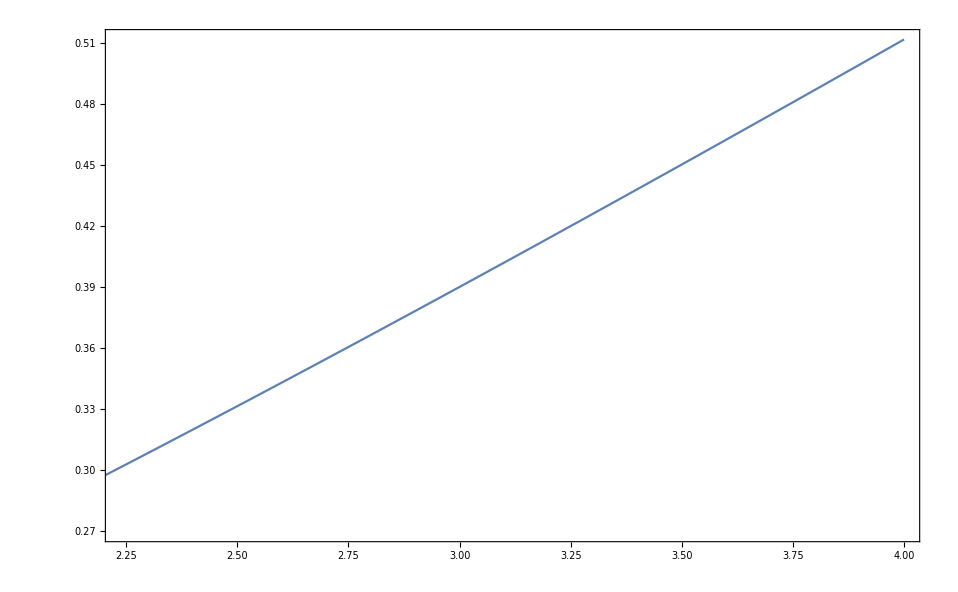

```mathematica
Plot[(9/2 outSMEFTrunner[[1]]^2)/(4 outSMEFTrunner[[3]]^3),{t,Log10[90],tHIGH},Frame->True,Axes->False,PlotRange->{{tLOW,tHIGH},Automatic}]
```